```mathematica
(*Vertices are labeled by {time index,Space index}*)
```

```mathematica
LabeledCycleLayer[n_,l_]:=Graph[Table[{l,i}<-> {l,1+Mod[i,n]},{i,n}]]
LabeledConnectionLayer[n_,l1_,l2_]:=Graph[Flatten[Table[{{l1,i}<-> {l2,i},{l1,i}<-> {l2,1+Mod[(i),n]}},{i,n}]]]
GenerateFlatSpaceTime[NumSpaceSlices_,NumTimeSlices_]:=Module[{},
SpatialSlices = Table[LabeledCycleLayer[NumSpaceSlices,i],{i,NumTimeSlices}];
ConnectorSlices = Table[LabeledConnectionLayer[NumSpaceSlices,i,Mod[i,NumTimeSlices]+1],{i,NumTimeSlices}];
graphComponents = Flatten[Join[SpatialSlices,ConnectorSlices]];
GraphUnion@@graphComponents
]
```

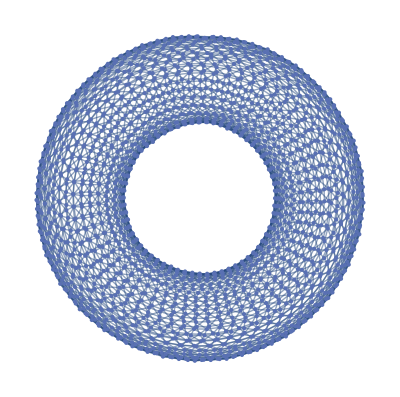

539.1678586

```mathematica
Start = AbsoluteTime[];
FlatSpace = GenerateFlatSpaceTime[64,32]
AbsoluteTime[]-Start
```

```mathematica
Move[SmallFlatSpace_]:=Module[{},
Edges = EdgeList[SmallFlatSpace];
Vertices = VertexList[SmallFlatSpace];

(*Chose a random Vertex *)
RV=RandomChoice[Vertices];

(*generate a spacetime with that vertex removed*)
vremoved = VertexDelete[SmallFlatSpace,RV];

(*generate a graph of the selected vertex and its adjacent edges*)
selectedSubGraph = GraphDifference[SmallFlatSpace,vremoved];
selectedSubGraph = VertexDelete[selectedSubGraph,_?(VertexDegree[selectedSubGraph,#]<1&)];

(*modify the selected subgraph*)
EL = EdgeList[selectedSubGraph];
VL = VertexList[selectedSubGraph];

TimeSliceIndex = RV[[1]];
PastTimeSliceIndex = Mod[TimeSliceIndex-2,TSMax]+1;
FutureTimeSliceIndex = Mod[TimeSliceIndex,TSMax]+1;

AdjacentEdges = Select[EL,Function[x,x[[1,1]]==TimeSliceIndex && x[[2,1]]==TimeSliceIndex]];
PastEdges = Select[EL,Function[x,x[[1,1]]==PastTimeSliceIndex]];
FutureEdges = Select[EL,Function[x,x[[2,1]]==FutureTimeSliceIndex]];

AdjacentEdge = Select[AdjacentEdges,Function[x,x[[1]]==RV]][[1]];
RandomPastEdge = RandomChoice[PastEdges];
RandomFutureEdge = RandomChoice[FutureEdges];

NV ={TimeSliceIndex, RV[[2]]+(AdjacentEdge[[2,2]]- RV[[2]])/10};

OldEdges = DeleteCases[EL,x_/;x==AdjacentEdge||x>700];
NewEdges = {RV<->NV ,NV<->AdjacentEdge[[2]],RandomPastEdge[[1]]<->NV,NV<->RandomFutureEdge[[2]]};

ModifiedSelectedSubGraph = Graph[Join[OldEdges,NewEdges]];



(*add the modified removed vertex subgraph back to the spacetime*)
GraphUnion[vremoved,ModifiedSelectedSubGraph]
]
```

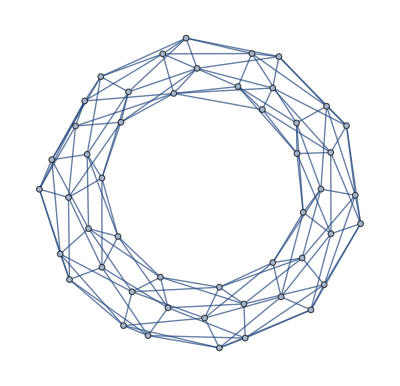

```mathematica
InverseMove[ST_]:=Module[{Edges,AdjacentVertices,RV,AdjacentVertex,Vertices,TimeSliceIndex},
Edges = EdgeList[ST];
Vertices = VertexList[ST];

(*Chose a random Vertex *)
RV=RandomChoice[Vertices];

TimeSliceIndex = RV[[1]];
AdjacentVertices = AdjacencyList[ST,RV];
AdjacentVertices = Select[AdjacentVertices,Function[x,x[[1]]==TimeSliceIndex ]];
AdjacentVertex = RandomChoice[AdjacentVertices];

SimpleGraph[Graph[DeleteCases[Vertices,RV],Edges/. RV-> AdjacentVertex]]

]
TSMax = 10;
SSMax =5;
SmallFlatSpace = GenerateFlatSpaceTime[SSMax,TSMax];
InverseMove[SmallFlatSpace]
```

```mathematica
NMoves[initialSpace_,n_]:=Nest[Move,initialSpace,n]
NInvMoves[initialSpace_,n_]:=Nest[InverseMove,initialSpace,n]
```

```mathematica
movedGraph = NInvMoves[NMoves[FlatSpace,25],25]
```

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

Part::partw: Part 2 of RandomChoice[{}] does not exist.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

Part::partw: Part 2 of RandomChoice[{}] does not exist.

$Aborted

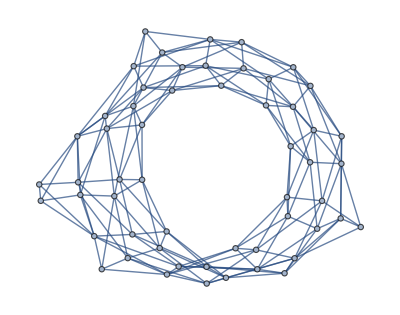

Module::lvsym: Local variable specification {Edges$,{{Vertices,TimeSliceIndex,AdjacentVertices}},RV$,AdjacentVertex$} contains {{Vertices,TimeSliceIndex,AdjacentVertices}}, which is not a symbol or an assignment to a symbol.

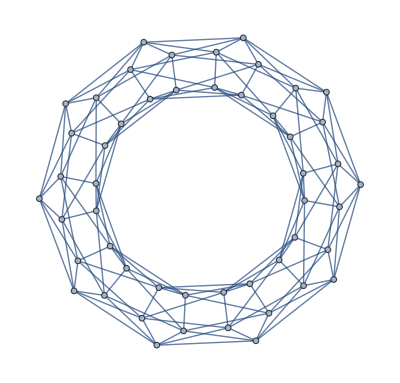
Module[{Edges$,{{Vertices,TimeSliceIndex,AdjacentVertices}},RV$,AdjacentVertex$},Edges$=EdgeList[-Graphics-];Vertices=VertexList[-Graphics-];RV$=RandomChoice[Vertices];TimeSliceIndex=RV$⟦1⟧;AdjacentVertices=AdjacencyList[RV$];AdjacentVertices=Select[AdjacentVertices,Function[x,x⟦1⟧==TimeSliceIndex]];AdjacentVertex$=RandomChoice[AdjacentVertices];SimpleGraph[Graph[DeleteCases[Vertices,RV$],Edges$/.RV$→AdjacentVertex$]]]

```mathematica
movedGraph = NMoves[SmallFlatSpace,5]
GG = EdgeDelete[SmallFlatSpace,Table[{i,1}<-> {i,2},{i,TSMax}]];
GraphPlot3D[movedGraph];
```

```mathematica
-Graphics-
"took 14 seconds to do 1000 inverse moves."
```

```mathematica
-Graphics-
"Takes ~9 minutes to generate"
```